```mathematica
SetDirectory[NotebookDirectory[]];
Get["LearningNewtonsMethod/LearningNewtonsMethod.m"];
SetOptions[EvaluationNotebook[],Background->None]
SetOptions[SelectedNotebook[], 
         System`BackgroundAppearance -> ConvertImageToFullyScaledNinePatch[-Graphics-]];
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideZero"}]]
Grid[{{ GoBack[slidePrima, 0], GoHomepage[slidePrima], GoForward[slidePrima, 1]}}, ItemSize->Fit]
```

-Graphics- | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslidePrimaButtonDataHyperlinkHyperlinkActive

# Il Metodo di Newton per l’approssimazione degli zeri di una funzione -Graphics- Anna Avena Matteo Sanfelici Giulia Cantini Roberto Ferraro Nicola Mainetti

```mathematica
CellPrint[Cell["", "", CellTags -> {"slidePrima"}]]
Grid[{{ GoBack[slideZero, 1], GoHomepage[slidePrima], GoForward[slideSeconda, 1]}}, ItemSize->Fit]
```

-Graphics-xr93z_shmslideZeroButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideSecondaButtonDataHyperlinkHyperlinkActive

## Outline

Presentazione del problema

Metodo di bisezione

Metodo delle secanti

Metodo di Newton

Funzionamento

Teoria

```mathematica
CellPrint[Cell["", "", CellTags->{"slideSeconda"}]]
Grid[{{ GoBack[slidePrima, 1], GoHomepage[slidePrima], GoForward[slideTerza, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslidePrimaButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideTerzaButtonDataHyperlinkHyperlinkActive

## Problema: ricerca di uno zero (soluzione) di una funzione

Ti sei mai chiesto come fa la calcolatrice a svolgere calcoli complicati come la radice sesta di 1221?

Questo problema è equivalente alla ricerca di uno zero della funzione  f (x) = x^(6^) - 1221
oppure della soluzione dell' equazione  x^(6^) - 1221 = 0.

```mathematica
Button[
"Nota bene!", 
MessageDialog["Una funzione f(x) è una relazione e ha senso considerarla per qualsiasi x \
che appartiene al suo dominio e quindi non solo per le x che sono zeri della funzione.\n\n
Un'equazione di incognita x invece è un'uguaglianza che risulta vera solo per le particolari x che sono sue soluzioni (dette \
radici) e non ha senso considerarla per x diverse da queste.", 
WindowTitle ->"La differenza tra funzioni ed equazioni"], 
Appearance -> Automatic, 
BaseStyle -> {"GenericButton", FontFamily -> "SourceSansPro", 30}, 
Evaluator -> Automatic, 
Method -> "Preemptive"]
(* TODO aumenta font all'interno della dialog *)
```

Nota bene!

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideTerza"}]]
Grid[{{ GoBack[slideSeconda, 1], GoHomepage[slidePrima], GoForward[slideQuarta, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideSecondaButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideQuartaButtonDataHyperlinkHyperlinkActive

## Ma come si trova la scrittura decimale di uno zero di f(x)?

Questo problema potrebbe essere irresolubile se il numero cercato fosse irrazionale e quindi avrebbe infinite cifre decimali.

Siamo però certi che è sempre possibile ottenere un’approssimazione anche con molte cifre decimali di un qualsiasi numero. 

Notando che la funzione  f (x) = x^(6^) - 1221  è continua e che f (3) < 0 e f (4) > 0 osservando il grafico risulta chiaro che uno zero di f si troverà tra 3 e 4.

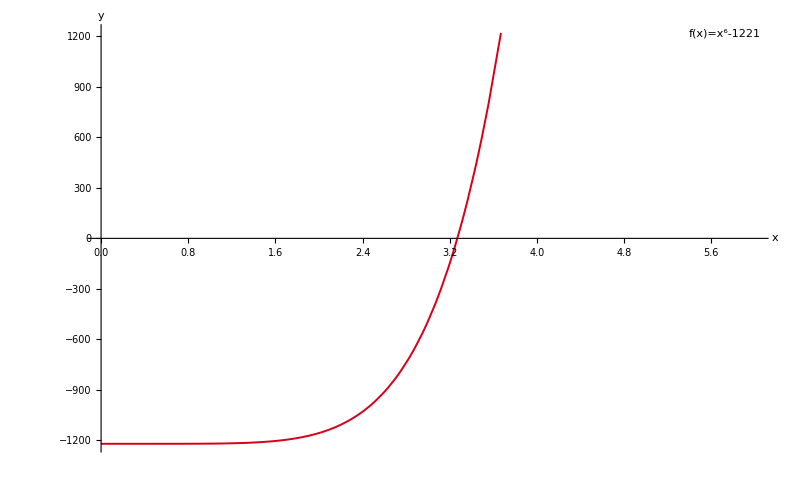

```mathematica
RootExampleGraphic[]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideQuarta"}]]
Grid[{{ GoBack[slideTerza, 1], GoHomepage[slidePrima], GoForward[slideQuinta, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideTerzaButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideQuintaButtonDataHyperlinkHyperlinkActive

Il ragionamento appena affrontato vale più in generale per qualunque funzione f(x) continua in un intervallo [a, b], che assume valori di segno opposto in a e b.

Data una funzione f (x) continua in un intervallo [a, b] tale che f (a) f (b) < 0 allora 
∃ c ∈ [a, b] tale che f (c) =0.

Vedremo di seguito 3 differenti metodi numerici per calcolare l’approssimazione dello zero cercato.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideQuinta"}]]
Grid[{{ GoBack[slideQuarta, 1], GoHomepage[slidePrima], GoForward[slideSesta, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideQuartaButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideSestaButtonDataHyperlinkHyperlinkActive

## Metodo di bisezione

Una tecnica per la ricerca di un’approssimazione dello zero all’interno di un intervallo [a, b] consiste nell’assumere come approssimazione dello zero di f(x) il valore medio dell’intervallo, cioè (a+b)/2.

```mathematica
BisectionInteractive[]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideSesta"}]]
Grid[{{ GoBack[slideQuinta, 1], GoHomepage[slidePrima], GoForward[slideSettima, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideQuintaButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideSettimaButtonDataHyperlinkHyperlinkActive

## Procedimento

### Passo 1

caso 1 :	 f ((a + b)/2) = 0   ⟶   a questo punto abbiamo trovato esattamente uno zero di f(x)

caso 2 :	 f ((a + b)/2) ha lo stesso segno di f(a)   ⟶   in questo caso possiamo ripetere il ragionamento precedente ed essere sicuri che lo zero si trovi in ((a + b)/2, b)

caso 3 :	 f ((a + b)/2) ha lo stesso segno di f(b)   ⟶   in questo caso possiamo ripetere il ragionamento precedente ed essere sicuri che lo zero si trovi in (a, (a + b)/2)

### Passo 2

Nei casi 2 e 3 ribattezziamo a e b gli estremi del nuovo intervallo (la cui ampiezza sarà la metà della precedente) e ritorniamo al passo 1.

### Passo 3

Quando la differenza tra a e b è minore dell’approssimazione voluta, assumiamo definitivamente come zero di f il valore  (a + b)/2.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideSettima"}]]
Grid[{{ GoBack[slideSesta, 1], GoHomepage[slidePrima], GoForward[slideOttava, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideSestaButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideOttavaButtonDataHyperlinkHyperlinkActive

## Metodo delle secanti

Un'altra tecnica per la ricerca dell’approssimazione dello zero consiste nell’assumere come valore approssimato dello zero del punto P = (x_1, y_1) di intersezione tra il segmento che unisce i punti (a, f(a)) e (b, f(b)) e l’asse x.
P è la soluzione del sistema:

```mathematica
Piecewise[{{y=0, }, {(x-a)/(b-a) = (y - f(a))/(f(b) - f(a)), }}]
```

0

Si ottiene x_1 = (f(a)(b-a))/(f(b)-f(a))

```mathematica
SecantAnimated[]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideOttava"}]]
Grid[{{ GoBack[slideSettima, 1], GoHomepage[slidePrima], GoForward[slideNona, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideSettimaButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideNonaButtonDataHyperlinkHyperlinkActive

## Passo 1

Calcolando f(x_1) possiamo trovare:

caso 1 :	f(x_1) = 0   ⟶   in questo caso abbiamo trovato esattamente uno zero di f(x)

caso 2 :	f(x_1) ha lo stesso segno di f(a)  ⟶   in questo caso possiamo ripetere il ragionamento precedente ed essere sicuri che lo zero si trovi in (x_1, b)

caso 3 :	f(x_1) ha lo stesso segno di f(b)   ⟶   in questo caso possiamo ripetere il ragionamento precedente ed essere sicuri che lo zero si trovi in (a, x_1)

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideNona"}]]
Grid[{{ GoBack[slideOttava, 1], GoHomepage[slidePrima], GoForward[slideDecima, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideOttavaButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideDecimaButtonDataHyperlinkHyperlinkActive

### Passo 2

Nei casi 2 e 3 ribattezziamo a e b gli estremi del nuovo intervallo e ritorniamo al passo 1.

### Passo 3

Quando la differenza tra a e b è minore dell’approssimazione voluta, assumiamo definitivamente come zero di f il valore x_1.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideDecima"}]]
Grid[{{ GoBack[slideNona, 1], GoHomepage[slidePrima], GoForward[slideUndici, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideNonaButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideUndiciButtonDataHyperlinkHyperlinkActive

## Metodo di Newton (o delle tangenti) :

L’ultima tecnica proposta per la ricerca dell’approssimazione dello zero consiste nell’assumere come valore approssimato dello zero l’ascissa del punto P = (x_1, y_1) di intersezione tra la retta r  tangente al punto (a, f(a)) e l’asse x.
La retta r ha coefficiente angolare f(a) e passa per il punto (a, f(a)) ed ha quindi equazione:

y - f (a) = f (a)(x-a)

P è la soluzione del sistema:

```mathematica
Piecewise[{{y = 0, }, {y - f(a) = f(a) (x-a), }}]
```

0

Si ottiene x_1 = a - (f(a))/(f'(a))

```mathematica
NewtonAnimated[]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideUndici"}]]
Grid[{{ GoBack[slideDecima, 1], GoHomepage[slidePrima], GoForward[slideDodici, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideDecimaButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideDodiciButtonDataHyperlinkHyperlinkActive

### Passo 1

## Calcolando f(x_1) possiamo trovare:

caso 1: f(x_1) = 0   ⟶   a questo punto abbiamo trovato esattamente uno zero di f(x)

caso 2: f(x_1) ≠ 0

### Passo 2

Nel caso 2 ribattezziamo a il valore x_1 e ritorniamo al passo 1.

### Passo 3

Quando la differenza tra x_1 ed a è minore dell’approssimazione voluta assumiamo definitivamente come zero di f il valore x_1.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideDodici"}]]
Grid[{{ GoBack[slideUndici, 1], GoHomepage[slidePrima], GoForward[slideTredici, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideUndiciButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideTrediciButtonDataHyperlinkHyperlinkActive

## Teoria

Il metodo delle tangenti, o metodo di Newton, può presentare delle problematiche.

Nell’ esempio qui a fianco si può notare che il metodo dà come seconda approssimazione dello zero un valore esterno al dominio della funzione e quindi non è possibile disegnare la seconda tangente per trovare una terza approssimazione.

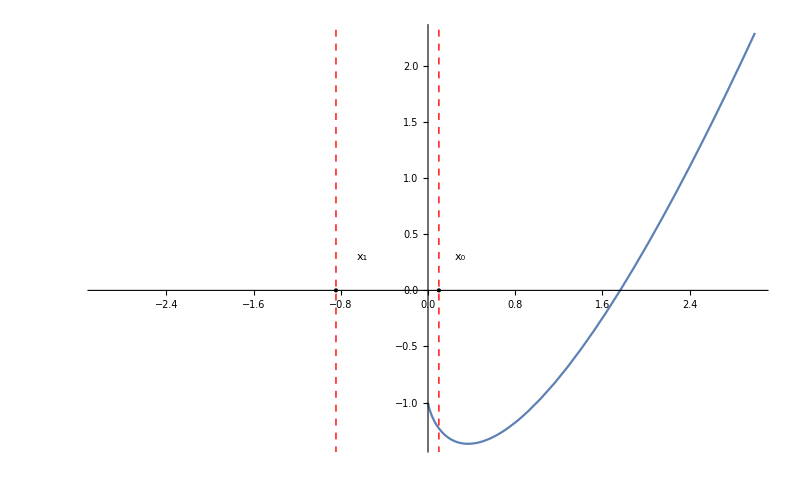

```mathematica
FirstExample[]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideTredici"}]]
Grid[{{ GoBack[slideDodici, 1], GoHomepage[slidePrima], GoForward[slideQuattordici, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideDodiciButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideQuattordiciButtonDataHyperlinkHyperlinkActive

In quest’altro esempio invece possiamo notare che non è possibile calcolare neanche una prima approssimazione dello zero x_1 = a - (f(a))/(f'(a)) poiché  f ’ (a)=0.

Geometricamente è possibile vedere ciò poiché la retta tangente al punto (0,1) è parallela all’asse delle x.

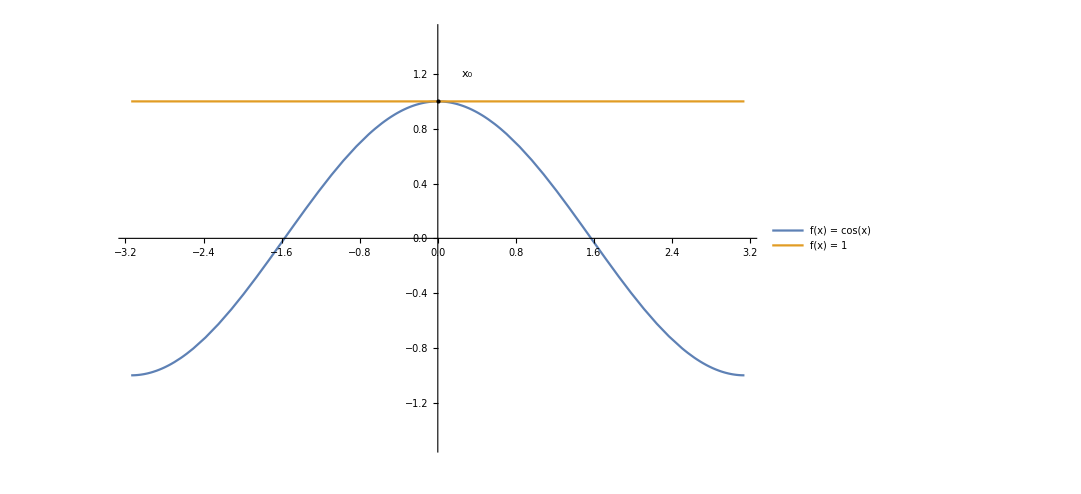

```mathematica
SecondExample[]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideQuattordici"}]]
Grid[{{ GoBack[slideTredici, 1], GoHomepage[slidePrima], GoForward[slideQuindici, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideTrediciButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideQuindiciButtonDataHyperlinkHyperlinkActive

Per ovviare a questi due possibili problemi possiamo limitarci ad usare questo metodo con opportune restrizioni.
Per prima cosa, come per tutti gli altri metodi, dobbiamo essere certi che esista uno zero, il che accade sempre se la funzione è continua ed assume valori sia positivi che negativi.

Inoltre chiediamo che il dominio della funzione sia tutto ℝ , per essere certi di non trovare mai approssimazioni dello zero che cadono fuori dal dominio.

Infine chiediamo che la funzione ammetta derivata prima e seconda (entrambe continue) e che la derivata prima, di volta in volta non si annulli nei punti assunti come approssimazione.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideQuindici"}]]
Grid[{{ GoBack[slideQuattordici, 1], GoHomepage[slidePrima], GoForward[slideSedici, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideQuattordiciButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideSediciButtonDataHyperlinkHyperlinkActive

Ma sotto queste restrizioni siamo certi che il metodo di Newton restituisca una soluzione vicina allo zero?

Per rispondere alla seguente domanda dimostriamo il seguente teorema.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideSedici"}]]
Grid[{{ GoBack[slideQuindici, 1], GoHomepage[slidePrima], GoForward[slideDiciassette, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideQuindiciButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideDiciassetteButtonDataHyperlinkHyperlinkActive

## Teorema 1

Data l' equazione f (x) = 0, sia z una radice ed x_1 un suo valore approssimato;

posto

F(x) = x - (f(x))/(f ' (x))

e calcolata la successione

x_i+ 1 = F(x_i) con i=1,2,...

se esiste un numero k < 1 tale che nell’intervallo che contiene i punti x_1,x_2,...,x_z risulta

|F'(x)|≤  k

allora

```mathematica
CellPrint@Cell[TextData[{Cell[BoxData[FormBox[StyleBox[RowBox[{UnderscriptBox["lim",RowBox[{"□","→","□"}]]," ","□"}],UnderscriptBoxOptions->{LimitsPositioning->False}],TraditionalForm]]]," "}],"Text"]
```

lim_(□→□) □

lim_(i→+∞) x_(1 = z)

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideDiciassette"}]]
Grid[{{ GoBack[slideSedici, 1], GoHomepage[slidePrima], GoForward[slideDiciotto, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideSediciButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideDiciottoButtonDataHyperlinkHyperlinkActive

## Dimostrazione

Per prima cosa proviamo F(z) = z

F(z) = z-(f(z))/(f ' (z))

ed essendo z una radice dell’equazione f(x) = 0 segue che f(z) = 0 e quindi

F(z) = z

Andiamo ora  a calcolare la distanza fra x_2 e z

x_2- z = F(x_1) - F(z)

Vogliamo applicare il teorema di Lagrange (o del valor medio) alla funzione F per ottenere

x_2- z = (x_1- z) * F'(x)

con x appartenente all’intervallo [ x_1, z ].

Per fare ciò dobbiamo dimostrare che la funzione F(x) rispetti le ipotesi del teorema di Lagrange.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideDiciotto"}]]
Grid[{{ GoBack[slideDiciassette, 1], GoHomepage[slidePrima], GoForward[slideDiciannove, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideDiciassetteButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideDiciannoveButtonDataHyperlinkHyperlinkActive

Per non appesantire la dimostrazione proveremo questo nel lemma successivo al teorema.

Usando l’ipotesi  |F'(x)|≤ k abbiamo

|x_2- z |≤ |x_1- z |* k

Iterando il ragionamento

|x_(i+1)- z |≤ |x_1- z |* (k^i)

Ed essendo k < 1 si ha

```mathematica
CellPrint@Cell[TextData[{Cell[BoxData[FormBox[StyleBox[RowBox[{UnderscriptBox["lim",RowBox[{"□","→","□"}]]," ","□"}],UnderscriptBoxOptions->{LimitsPositioning->False}],TraditionalForm]]]," "}],"Text"]
```

lim_(□→□) □

lim_(i→ +∞) |x_(i+1)-z|

e quindi

```mathematica
CellPrint@Cell[TextData[{Cell[BoxData[FormBox[StyleBox[RowBox[{UnderscriptBox["lim",RowBox[{"□","→","□"}]]," ","□"}],UnderscriptBoxOptions->{LimitsPositioning->False}],TraditionalForm]]]," "}],"Text"]
```

lim_(□→□) □

lim_(i→+∞)  x_i=z

c.v.d

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideDiciannove"}]]
Grid[{{ GoBack[slideDiciotto, 1], GoHomepage[slidePrima], GoForward[slideVenti, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideDiciottoButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideVentiButtonDataHyperlinkHyperlinkActive

## Lemma

La funzione F(x) del teorema precedente rispetta le ipotesi del teorema di Lagrange nell’intervallo che contiene i punti x_1,x_2,...,x_z.

## Dimostrazione

Ricordiamo che le ipotesi del teorema di Lagrange sono: la funzione continua e la funzione derivabile in tutto l’intervallo al più escludendo gli estremi.

F(x) = x-(f(x))/(f'(x))

f(x) è stata supposta all’inizio di questo paragrafo.

Analogamente f'(x) è stata supposta continua e non nulla nei punti che ci interessano.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideVenti"}]]
Grid[{{ GoBack[slideDiciannove, 1], GoHomepage[slidePrima], GoForward[slideVentuno, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideDiciannoveButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideVentunoButtonDataHyperlinkHyperlinkActive

Quindi (f(x))/(f'(x)) è una funzione continua e lo è anche la funzione F(x) in quanto somma di funzioni continue.

F'(x) =1-{(f'(x)^2-f(x)f'(x))/(f'(x)^2) }

= 1- 1+{ (f(x)f'(x))/(f'(x)^2) }

= { (f(x)f'(x))/(f'(x)^2)  }

F(x) è derivabile se (f(x)f'(x))/(f'(x)^2) è continua nell’intervallo che ci interessa; essendo f(x) ed f '(x) continue, come supposto ad inizio paragrafo, ed essendo f ‘(x) ≠ 0 ciò risulta vero.

c.v.d

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideVentuno"}]]
Grid[{{ GoBack[slideVenti, 1], GoHomepage[slidePrima], GoForward[slideVentidue, 1]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideVentiButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-xr93z_shmslideVentidueButtonDataHyperlinkHyperlinkActive

Grazie a questo teorema e a questo lemma possiamo essere certi che per qualsiasi funzione, purché con le opportune restrizioni dette, ci è possibile trovare una approssimazione di un suo zero con il metodo delle tangenti di Newton.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideVentidue"}]]
Grid[{{ GoBack[slideVentuno, 1], GoHomepage[slidePrima], GoForward[slideVentitre, 0]}}, ItemSize -> Fit]
```

-Graphics-xr93z_shmslideVentunoButtonDataHyperlinkHyperlinkActive | -Graphics-xr93z_shmslidePrimaButtonData | -Graphics-

```mathematica
ReadInputFile[]
```

Nuovo Esercizio